```mathematica
p = Predict[ExampleData[{"MachineLearning", "BostonHomes"},"TrainingData"], PerformanceGoal->"Quality"]
```

PredictorFunction[…]

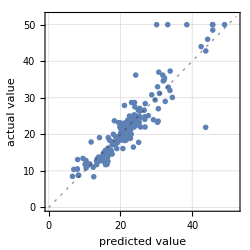
Predictor Measurements
Predictor method | GradientBoostedTrees
Number of test examples | 168
Standard deviation | 3.91 ± 0.54
Standard deviation baseline | 8.98 ± 0.71
R-squared | 0.81 ± 0.06
Mean cross entropy | 4.02 ± 0.7
Single evaluation time | 7. ms/example
Batch evaluation speed | 1.15 examples/ms
-Graphics- |

```mathematica
pm=PredictorMeasurements[p,ExampleData[{"MachineLearning", "BostonHomes"},"TestData"]]
```

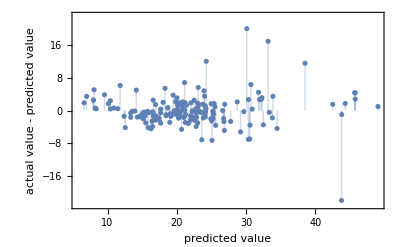

```mathematica
pm["ResidualPlot"]
```

```mathematica
pm["StandardDeviation"]
```

3.91293

```mathematica
p2 = Predict[ExampleData[{"MachineLearning", "BostonHomes"},"TrainingData"], Method->"RandomForest", PerformanceGoal->"Quality"]
```

PredictorFunction[…]

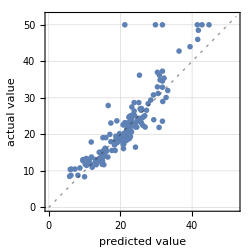
Predictor Measurements
Predictor method | RandomForest
Number of test examples | 168
Standard deviation | 4.35 ± 0.69
Standard deviation baseline | 8.98 ± 0.71
R-squared | 0.766 ± 0.083
Mean cross entropy | 2.91 ± 0.21
Single evaluation time | 7.03 ms/example
Batch evaluation speed | 1.58 examples/ms
-Graphics- |

```mathematica
pm2=PredictorMeasurements[p2,ExampleData[{"MachineLearning", "BostonHomes"},"TestData"]]
```